#### gr. 1

Zad. 1

```mathematica
Together[1/x-3/x^2+5/(2x-3)];
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(9-9 x+7 x^2)/(-3 x^2+2 x^3)

3/x+5/2 Log[3-2 x]+Log[x]

Zad. 2

{{x→-1},{x→2}}

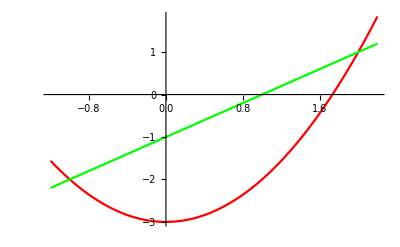

9/2

```mathematica
y1=x^2-3;
y2=x-1;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1.2,2.2},PlotStyle->{Red,Green}]
Integrate[y2-y1,{x,-1,2}]
```

Zad. 3

```mathematica
z=x^3-2x y+y^2-3x+2y;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-3+3 x^2-2 y

2-2 x+2 y

{{x→-1/3,y→-4/3},{x→1,y→0}}

{-8,8}

{-2,6}

#### gr. 2

Zad. 1

```mathematica
Together[2/(x+1)+(x-3)/(x^2+1)]
Integrate[%,x]//Expand
```

(-1-2 x+3 x^2)/((1+x) (1+x^2))

-3 ArcTan[x]+2 Log[1+x]+1/2 Log[1+x^2]

Zad. 2

```mathematica
π Integrate[(2x-1)^2,{x,1,2}]
```

(13 π)/3

Zad. 3

```mathematica
z=-x^2+x y^2-y^3-4 x;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-4-2 x+y^2

2 x y-3 y^2

{{x→-3/2,y→-1},{x→-2,y→0},{x→6,y→4}}

{-10,8,-40}

{-2,-2,-2}